## MergeEdges-example.nb

Example Cellzilla2D notebook

GPL License applies.
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 21:01:58
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

```mathematica
w=TemplateRandom[15, {{0,0}, {10,0}, {11, 10}, {-1, 10}}];
```

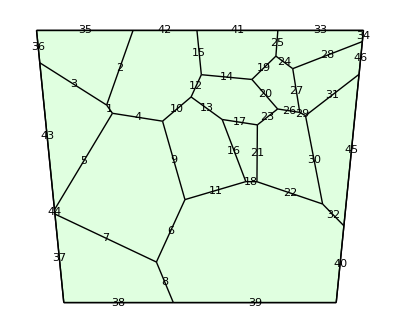

```mathematica
ShowTissue[w, "EdgeNumbers"-> True]
```

```mathematica
e=TissueEdges[w]
```

{{1,2},{1,25},{1,26},{2,4},{2,27},{3,5},{3,28},{3,29},{4,5},{4,6},{5,9},{6,7},{6,8},{7,10},{7,24},{8,9},{8,12},{9,11},{10,13},{10,14},{11,12},{11,18},{12,14},{13,15},{13,23},{14,16},{15,16},{15,32},{16,17},{17,18},{17,31},{18,30},{19,23},{19,32},{20,25},{20,26},{21,28},{21,29},{22,29},{22,30},{23,24},{24,25},{26,27},{27,28},{30,31},{31,32}}

```mathematica
Intersection[e[[10]], e[[12]]]
```

{6}

```mathematica
Complement[Flatten[First/@Position[e,#]&/@Intersection[e[[10]], e[[12]]]], {10,12}]
```

{13}

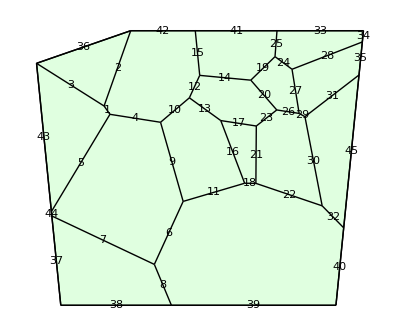

```mathematica
w1=MergeEdges[w,36,35];
ShowTissue[w1, "EdgeNumbers"-> True]
```